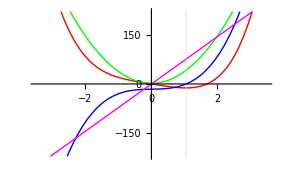

```mathematica
Clear[x]; 
(* IMPORTANT! Otherwise, wrong result when evaluating total notebook *)
Plot[{x^2 + 3 x^4-16x,2x+12 x^3-16,2+36 x^2,72x},
{x, -3.5, 3.5}, PlotStyle->{Red,Blue,Green,Magenta},
GridLinesStyle->LightGray,GridLines->{{1.05},None},
PlotRange->{{-3.5, 3.5},{-220, 220}},
PlotRangeClipping -> True]
```

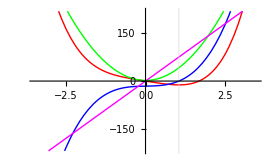

```mathematica
f[x_]:=x^2+3 x^4-16x;
Plot[{f[x], f'[x], f''[x],f'''[x]}, {x, -3.5, 3.5},
PlotStyle->{Red,Blue,Green,Magenta},
GridLinesStyle->LightGray,GridLines->{{1.05},None},
PlotRange->{{-3.5, 3.5},{-220, 220}},
PlotRangeClipping -> True]
```

```mathematica
{∫_0^4 (3 x^2+x+16)ⅆx, 
(3/3 4^3+1/2 4^2+(16*4))- (3/3 0^3+1/2 0^2+(16*0)),
(64+8+64)-(0+0+0)}
```

{136,136,136}

```mathematica
{N[∫_0^4 x^2 ⅆx], N[(1/3 4^3)- (1/3 0^3)],0.333333*64}
```

{21.3333,21.3333,21.3333}

```mathematica
{N[∫_-2^1 3 x^5 ⅆx], N[(3/6 1^6)- (3/6(-2)^6)], 0.5-32}
```

{-31.5,-31.5,-31.5}

```mathematica
{∫x^2 ⅆx, 1/3 x^3}
```

{x^3/3,x^3/3}

```mathematica
{∫(4 x^2+x^3)ⅆx, 4/3 x^3+1/4 x^4}
```

{(4 x^3)/3+x^4/4,(4 x^3)/3+x^4/4}